# Skeleton Analysis of Melt Network

## Functions

```mathematica
Clear["Global`*"];
```

getRange[list] returns the range(min and max value) of elements in the list:

```mathematica
getRange:=Function[list,
	min = Min[list];
	max = Max[list];
	{min, max}]
```

move[from, to] add an offset to list from based on the distance between center of range2 and range1:

```mathematica
move:=Function[{from,to},
	range1 = getRange[from];
	range2 = getRange[to];
	offset = (range2⟦1⟧ + range2⟦2⟧-range1⟦1⟧ - range1⟦2⟧)/2;
	res = from + offset;
	res]
```

coordsAlign[coords1, coords2] add offsets to each dimension of coords1 so that coords1 is aligned with coords2. coords1, coords2: N by 3(x,y,z)

```mathematica
coordsAlign:=Function[{coords1,coords2},
	newX = move[coords1⟦;;,1⟧,coords2⟦;;,1⟧];
	newY = move[coords1⟦;;,2⟧,coords2⟦;;,2⟧];
	newZ = move[coords1⟦;;,3⟧,coords2⟦;;,3⟧];
	newCoords1 = {newX,newY,newZ};
	Transpose[newCoords1]]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
getJunctions:=Function[{graph},
	ans={};
	For[i=1,i≤VertexCount[graph],i++,
	(*If[Length[AdjacencyList[graph,i]]>2,AppendTo[ans,{i,Length[AdjacencyList[graph,i]]}]]];*)
	degree = VertexDegree[graph,i];
	If[degree>2,AppendTo[ans,{i,degree}]]];
	ans
]
```

mergeScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {{x1,y1,z1},r1} 
	ball2: {{x2,y2,z2},r2}

```mathematica
mergeScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦2⟧,ball2⟦2⟧];
	r2 = Min[ball1⟦2⟧,ball2⟦2⟧];
	d = EuclideanDistance[ball1⟦1⟧, ball2⟦1⟧];
	score = (r1 + r2 - d)/(2*r2);
	score
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	If[VertexDegree[graph, v] ≠ 2, Return[resGraph]];
	
	neighbors = AdjacencyList[resGraph,v];
	v1 = neighbors⟦1⟧;
	v2 = If[Length[neighbors] == 2,neighbors⟦2⟧, neighbors⟦1⟧];
	
	resGraph = VertexDelete[resGraph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
simplifyGraph := Function[{skelGraph},
	g = skelGraph;
	nodesDeg2 = Pick[VertexList[g], VertexDegree[g], 2];
	
	While[Length[nodesDeg2] > 0,
		g = deleteNode[g, nodesDeg2⟦1⟧];
		nodesDeg2 = Drop[nodesDeg2,1];
	];
	g
]
```

mergeJunctions[ball1,ball2] merges ball1 and ball2
graph: the simplified graph showing connectivity relationship of junctions
ball:{identifier, degree, {x,y,z},r}

```mathematica
mergeJunctions:= Function[{graph, ball1, ball2},
	v1 = ball1⟦1⟧;
	v2 = ball1⟦2⟧;
		
]
```

## Function Test

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

{5,6.5,7.7,8}

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
(*testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};*)
testLines = {{1,2},{1,2}};
g = linesToGraph[testLines];
GraphPlot3D[g]
VertexDegree[g,1]
EdgeList[g]
(*FindPath[g,2,3, Infinity, All]
s = EdgeContract[g,1<->3];
GraphPlot3D[s]*)
```

-Graphics3D-

2

{1<->2,1<->2}

test deleteNode[graph, v], simplifyGraph[graph]

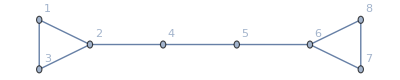

-Graphics3D-

{2<->2,2<->6,6<->6,6<->2,2<->6}

{2<->2,2<->6,6<->2,2<->6}

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
s = simplifyGraph[g];
s = EdgeAdd[g,6<->2];
s = EdgeAdd[s,2<->6];
GraphPlot3D[s]

EdgeList[s]
s = EdgeDelete[s,6<->6];
(*s = EdgeDelete[s,2<->2];*)
EdgeList[s]
s = VertexContract[s,{2,6}];
EdgeList[s]
GraphPlot3D[s]

(*k = Graph[{1<-> 2, 2 <-> 1, 2 <-> 1}, VertexLabels -> "Name"]
VertexContract[k,{1,2}]*)
```

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

```mathematica
i = 0;
While[i<10,Print[i];i++]
```

0

1

2

3

4

5

6

7

8

9

## Code

### Set working directory

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

### Import data from files

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

```mathematica
maRawData = Import["data\\scoba12_small.ply","Table"];
maTable = maRawData⟦15;;,;;⟧;

maPoints = maTable⟦;;86117,;;⟧;
maPolygons = maTable⟦363203;;,10;;12⟧ + 1;
```

```mathematica
numOfPoints = 12326;
numOfEdges = 12468;

skelRawData = Import["data\\scoba12_small_skel_0.1.ply","Table"];
skelTable = skelRawData⟦15;;,;;⟧;

skelPoints = skelTable⟦;;numOfPoints,3;;5⟧;
skelLines = skelTable⟦numOfPoints+1;;⟧ + 1;
skelRadius = skelTable⟦;;numOfPoints,2⟧;
```

align coordinates

```mathematica
maPoints = coordsAlign[maPoints,skelPoints];
```

### Processing data of scoba12 and skeletons

#### Ground Truth

trueJunctions: N by 5 (x, y, z, CN, diameter)

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

#### Median Axes

```mathematica
polygonInCoords = Table[{Blue,Polygon[{maPoints⟦maPolygon⟦1⟧⟧,maPoints⟦maPolygon⟦2⟧⟧,maPoints⟦maPolygon⟦3⟧⟧}]},{maPolygon,maPolygons}];
```

#### Skeleton data

```mathematica
skelGraph = linesToGraph[skelLines];
(*simplifiedGraph = simplifyGraph[skelGraph]*)
junctions = getJunctions[skelGraph];
junctionBalls = Table[{Ball[skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧]},{i,Dimensions[junctions]⟦1⟧}];
junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧},{i,Dimensions[junctions]⟦1⟧}]
```

{{2,3,{-4.5,2.5,1.5},1.66304},{52,3,{-46.5,23.5,-54.5},2.77617},{117,3,{38.5,-53.5,7.5},0.866025},{134,3,{49.5,10.5,39.5},0.866025},{158,3,{26.5,17.25,36},2.26377},{161,5,{49.5,4.5,44.5},0.866025},{172,3,{51,26.5,36},1.26217},{203,3,{54.5,-0.5,45.5},1.3629},{215,3,{55.5,0.5,41.5},1.35553},{223,3,{-6.5,41.5,-65.5},2.98333},{230,3,{52.5,-20.5,-43.5},1.77939},{231,3,{36.5,-21.5,-32.5},2.16798},{246,3,{41.5,-18.5,-30.5},1.02813},{271,3,{21.5,-41.5,-1.5},1.47822},{300,3,{-25.5,-37.5,-4.5},0.992027},{358,3,{-36.5,-13.5,-11.5},1.55249},{376,3,{-53.5,14.5,-43.5},1.78295},{429,3,{-51.5,58.5,-63.5},1.60101},{439,3,{-43.5,50,-65},1.02813},{442,3,{-48.5,43.5,-56.5},0.992027},{457,3,{-54.5,37.5,-47.5},0.992027},{506,3,{-54.5,37.5,-48.5},1.26217},{534,3,{-14.5,7.5,24.5},0.992027},{547,3,{-13.5,7.5,24.5},1.49367},{595,3,{-47,-12,61},1.3171},{633,3,{-45.5,-55.5,65.5},2.11552},{684,3,{-11.5,6.5,25.5},1.07039},{712,3,{21.5,-39.5,0.5},1.26217},{715,3,{17.5,-35.5,-1.5},1.44152},{723,3,{23.5,-42.5,1.5},1.32915},{775,3,{53,-26.5,45},0.933012},{818,3,{54,-22.5,42},1.07311},{846,3,{54.5,1.5,41.5},0.992027},{854,3,{52.5,28.5,60.5},1.17139},{865,3,{46.5,17.5,39.5},1.02813},{885,3,{50,7.5,43},1.20748},{890,3,{48.5,13.5,38.5},1.31324},{893,3,{48.5,8.5,42.5},0.933012},{899,3,{50.5,10.5,38.5},1.44145},{901,3,{54.5,3.5,39.5},1.875},{908,3,{50.5,7.5,45.5},2.33074},{914,3,{44.3571,5.3571,43.929},0.992027},{946,3,{46.5,7.5,42.5},1.17139},{960,3,{23.5,8.5,36},1.17139},{973,3,{32.5,10.5,38.5},1.97504},{1056,3,{32.5,56.5,19.5},0.933012},{1103,3,{32.5,35.5,29},0.992027},{1156,3,{53.5,9.5,35.5},1.47707},{1179,3,{52.5,-19.5,-43.5},1.02813},{1248,3,{-47.5,36.5,-54.5},1.72184},{1252,3,{32.1667,46.5,-5.8333},0.933012},{1283,3,{45.5,-24.5,-46.5},0.992027},{1302,3,{38.5,-26.5,-45.5},1.19828},{1309,3,{42.5,-25.5,-46.5},1.44152},{1310,3,{43.5,-23.5,-45.5},0.866025},{1314,3,{48.5,-19.5,-39.5},1.82247},{1318,3,{47.5,-20.5,-43.5},1.26217},{1332,3,{50.9,-45.9,-26.5},0.701587},{1346,3,{37,-27,-45},1.07311},{1347,3,{42.5,-24.5,-45.5},1.4401},{1349,3,{40.5,-27.5,-47.5},1.34728},{1383,3,{36.1667,-21.8333,-31.8333},1.17139},{1391,3,{38.5,9.5,-14.5},0.866025},{1410,3,{12.5,-49.5,-8},1.47822},{1415,3,{-8.3,-54.1,-8.9},0.866025},{1438,3,{20.5,-40.5,-2.5},0.992027},{1465,3,{19,-39,-3},1.96497},{1467,3,{19.5,-39.5,-2.5},1.07311},{1490,3,{35.5,-43.5,-34.5},2.08346},{1564,3,{43.5,-45.5,-46.5},1.02813},{1574,3,{42.5,-47.5,-43.5},0.992027},{1584,3,{38.5,-30,-49},2.07221},{1601,4,{42.5,-37.5,-61.5},1.65831},{1602,3,{47.714,-39.3571,-57.5},1.69968},{1668,3,{-50.5,-36.9286,-37.0714},1.26217},{1717,3,{-42.5,-56.5,2.5},1.74402},{1726,3,{-32.5,-57.5,-7.5},2.56465},{1729,3,{-33.5,-50.5,-9.5},2.20302},{1814,3,{-26.5,-39.5,-3.5},1.50505},{1817,3,{-28.5,-52.5,-11.8333},1.98835},{1841,3,{-13.5,-50.5,-10},0.933012},{1924,3,{-10.25,-13.5,-5.6667},0.59512},{1990,3,{-40.5,-11.5,-14.5},3.12534},{2005,3,{-48.7,-9.22,-18.78},1.02813},{2023,3,{-50.75,-8,-11.5},1.85754},{2041,3,{-52.4,-17.2,-24.6},1.10487},{2087,3,{-50,-22,-27},2.02346},{2106,3,{-50.5,-8.5,-23},3.01816},{2121,3,{-52,-2.5,-28},1.19911},{2134,3,{-51.2143,-3.5,-25.7857},1.15413},{2168,3,{-44.5,24,-58.5},1.21745},{2199,3,{-54.5,45.5,-52.5},1.36007},{2205,3,{-46.7,23.7,-52.7},1.26217},{2209,3,{-45,15.5,-49},1.28019},{2250,3,{-50,22,-46.5},0.866025},{2251,3,{-49.3,22.4,-48.4},0.866025},{2254,3,{-54.5,39.5,-48.5},1.26217},{2291,3,{-53.5,6.5,-37.8333},1.11803},{2364,3,{-37.9,27.1,-60.4},2.10838},{2441,3,{-22.7105,23.7632,-59.1316},1.17247},{2502,3,{-49.5,40.5,-54.5},1.40623},{2569,3,{-6.0455,43.136,-39.8636},0.992027},{2581,3,{-52.5,45.5,-55.5},1.54079},{2588,3,{-21.1154,51.5,-66.4231},1.30383},{2645,3,{-45.5,49.5,-64.5},2.66032},{2652,3,{-48.5,55.5,-65},1.90444},{2666,3,{-52.5,53.5,-60.5},2.70947},{2671,3,{-51.5,48.5,-58.5},2.03448},{2678,3,{-53.5,54.5,-60.5},1.81164},{2699,3,{-49,48.5,-60},2.03206},{2702,3,{-52.5,46.5,-56.5},2.44296},{2707,3,{-51.5,44.5,-55.5},2.27209},{2714,3,{-48,44,-58},2.56025},{2726,3,{-46.5,42.5,-58.5},2.00814},{2741,3,{-44,37,-58},1.94881},{2747,3,{-43.5,50.5,-65.5},1.36178},{2757,4,{-45.5,35.5,-54.5},1.76457},{2767,3,{-49.5,39.5,-53.5},3.3335},{2772,3,{-49.5,37.5,-52.5},1.26189},{2775,3,{-54.5,43.5,-52.5},0.933012},{2778,3,{-49.5,41.5,-55.5},1.76171},{2780,3,{-50.5,38.5,-52.5},1.11803},{2781,3,{-51.5,44.5,-54.5},1.43542},{2783,3,{-50.5,41.5,-54.5},0.933012},{2787,3,{-53.5,37.5,-48.5},2.23537},{2788,3,{-53.5,41.5,-52.5},2.25357},{2846,3,{-47.5,34.5,-52.5},0.992027},{2866,3,{-51.5,42.5,-53.5},2.12989},{2868,3,{-50.5,39.5,-53.5},2.41707},{2869,3,{-48.5,36.5,-52.5},1.93888},{2985,3,{-14.9925,19.0075,-26.8582},0.866025},{2989,3,{-16.2333,25.5667,-18.5},0.992027},{3055,3,{-31,16.5,-26.5},1.72239},{3111,3,{-49.54,-1.5,-23.9},1.11803},{3117,3,{-51.5,2.5,-32.5},1.65831},{3132,3,{-48,5.25,-33},1.20096},{3174,3,{-54,14,-1},3.2437},{3188,3,{-51.8333,15.1667,-15.5},2.95186},{3220,3,{-55,11.5,14},1.02813},{3382,3,{-18.5,9.5,24.5},1.76457},{3384,3,{-22.5,9.5,22.5},0.933012},{3418,3,{-14.5,6.5,23.5},0.866025},{3426,3,{-21.5,7.5,21},1.93221},{3454,3,{-15.1667,4.8333,19.5},2.2394},{3498,3,{-27.4231,18.5,26.0385},0.866025},{3522,3,{-24.9,18.1,26.9},1.23216},{3643,3,{-38.1667,36.5,46.167},2.18913},{3707,3,{-12.3333,48,36.333},1.26217},{3773,3,{-18.9,33.9,40.5},1.02813},{3809,3,{-24,29,38.5},2.28152},{3815,3,{-24.9545,27.9545,36.045},1.44338},{3820,3,{-17.5,32.6154,42.654},0.992027},{3822,3,{-19.7857,31.4048,40.881},2.03645},{3828,3,{-12.5,31.5,50.5},1.89572},{3884,3,{-36,-6.5,59},2.09982},{3903,3,{-26.9,24.9,42.5},0.729298},{3969,3,{-36.5,-3.5,56.5},0.933012},{3999,3,{-41.2273,0.863602,41.773},1.8},{4099,3,{-48.5,-25,70},0.992027},{4117,3,{-43.5,-52.5,66.5},2.57127},{4205,3,{-51.5,-56,7.5},1.19911},{4232,3,{-39.5667,-45.3,13.1667},0.992027},{4291,3,{-49.3333,-9.3333,14.3333},1.47891},{4308,3,{-46.0714,-0.9286,22.6429},1.53053},{4360,3,{-39.1765,-17.0294,16.4118},2.16964},{4420,3,{-39.875,-16.125,16.25},1.94408},{4440,3,{-14.8333,-21.1667,-1.5},1.23352},{4455,3,{-25.5,-16.8333,0.5},1.14012},{4487,3,{-8.3571,0.214298,15.6429},1.38817},{4495,3,{-7.4231,-0.115398,13.0385},1.11803},{4564,3,{20.5,-37.5,-0.5},1.02813},{4573,3,{22.5,-41.5,0.5},1.24975},{4597,3,{35.1,-54.1,10.8},1.17139},{4601,3,{35.7,-54.5,12.3},0.992027},{4619,3,{37.5,-45.5,21.5},1.24975},{4661,4,{37.9118,-31.4412,42.618},1.68385},{4795,3,{53.5,6.5,37.5},1.38817},{4812,3,{51.5,7.5,41.5},2.30663},{4816,3,{49.5,9.5,44.5},1.19024},{4830,3,{47.5,14,38.75},1.30222},{4845,3,{24.5,8.5,36},1.29393},{4882,3,{18.5,9.5,35.167},1.26217},{4884,3,{11.5,11.5,37.5},1.20749},{4887,3,{13.5,16.5,38.5},0.992027},{4935,3,{27.8333,25.8333,38.1},1.26217},{4952,3,{25.5,30.5,38.5},1.23521},{4962,3,{29.5,33.5,32.5},1.02813},{4988,3,{6,42.5,46.5},1.76457},{5099,3,{50.5,31.5,34.5},4.51962},{5100,3,{38.6667,35.6667,18.3333},3.40768},{5181,3,{34.75,34,4.75},1.11237},{5189,3,{40.3571,34.3571,17.6429},1.07311},{5206,3,{26.5,18.5,35.9},1.17139},{5241,3,{16.5,8.7727,34.682},1.10517},{5311,3,{52.5,15.5,35.5},1.19911},{5317,3,{42.5,7.5,-16.5},0.866025},{5324,3,{47,12.5,-16},0.992027},{5358,3,{28.5,25.5,-6},1.65831},{5359,4,{28.5,26.5,-5.5},2.18886},{5374,3,{40.5,11.5,-14.5},1.11803},{5382,3,{38.5,9.5,-15.5},1.36827},{5423,3,{-1.3621,7.1897,-14.6379},2.38764},{5525,3,{36,44.5,-8},1.26217},{5568,3,{48.5,-20.5,-42.5},1.41241},{5582,3,{36,-23.5,-38},0.992027},{5586,3,{40.5,-26.5,-46.5},0.992027},{5596,3,{37.5,-30.5,-48.5},1.15413},{5702,3,{3.2692,-2.4231,-18.8846},1.73055},{5710,3,{1.5,-36.5,-5.3},0.992027},{5735,3,{4.5,-40.5,-6.1667},1.11237},{5786,3,{18.5,-56.3,-7.3},0.933012},{5796,3,{23.5,-48.5,-14.5},1.02813},{5832,3,{19.5,-37.5,-1.5},0.933012},{5859,3,{32.5,-44.5,-30.5},0.576387},{5873,3,{35,-41,-30.5},1.02813},{5879,3,{35.1,-40.9,-28.7},1.47822},{5890,3,{33.0556,-41.1667,-25.5},0.59512},{5893,3,{33.1364,-41.0455,-26.1818},1.72602},{5908,3,{26.5,-51.5,-17.5},1.65831},{5910,3,{26,-51,-16},2.01554},{5919,3,{34.5,-57.5,-7.5},2.08573},{6018,3,{40.5,-38.5,-54.5},3.50419},{6068,3,{48.1667,-21.5,-44.1667},1.22474},{6079,3,{51.1667,-23.3333,41.3333},0.866025},{6135,3,{47.1357,32.2952,-10.431},0.866025},{6172,3,{-51.5,56.8333,-63.1667},0.866025},{6181,3,{-24.8958,23.6458,-59.7083},1.65831},{6196,3,{47.8333,-22.5,-45.1667},1.11803},{6281,3,{53.6667,-26,45.6667},0.866025},{6413,3,{51.5,24.8333,35.1667},0.866025},{6448,3,{-7.21153,42.654,-41.9423},0.866025},{6452,3,{43.8333,-46.5833,-44.8333},0.866025},{6478,3,{36.1667,-22.8333,-36.8333},1.11803},{6512,3,{44.1667,-23.8333,-45.5},0.866025},{6525,3,{51.125,-47.7813,-27.1875},2.3585},{6539,3,{49.8333,-23.5,-45.8333},0.866025},{6548,3,{51.1667,-21.5,-44.8333},2.06155},{6743,3,{-45.5,36.8333,-55.8333},2.54951},{6883,3,{-31.8333,29.3333,-62.3333},1.28019},{6910,3,{-54.8333,43.5,-50.8333},0.866025},{6921,3,{-1.5,43.167,-17.3333},1.78536},{6952,3,{-13.3359,18.6179,-26.1154},0.866025},{6978,3,{-2.73335,6.3,-16.9333},1},{7012,3,{-52.3,2.8,-33.2},1.49733},{7041,3,{-55.3333,6.83333,15.6667},0.866025},{7068,3,{-18.5,9.16667,23.8333},0.866025},{7080,3,{-26.0178,16.8036,25.6964},1.61803},{7114,3,{-11.6111,3.16667,17.4444},0.866025},{7129,3,{21.1667,52.8333,22.5},1.41421},{7173,3,{-6.91665,29.6666,46.75},1},{7230,3,{-53.8333,12.3333,15},0.866025},{7240,3,{-40.7333,0.9,40.6},1.11803},{7263,3,{25,-4.33333,39.3333},1.5459},{7284,3,{-44.1048,-28.2857,68.9033},0.866025},{7304,3,{-48.8333,-56.5,8.72223},1.22474},{7386,3,{-10.5833,-15,1.83333},1.29904},{7482,3,{37.1667,-52.1667,23.5},0.866025},{7591,3,{43.8333,-27.9444,42.389},1},{7606,3,{40,12.8334,38.8335},1.11803},{7624,3,{53.1667,0.833333,45.1667},0.866025},{7685,3,{48.8333,8.5,42.1667},1.11803},{7716,3,{44.5,4.5,44},1.11803},{7720,3,{50.3333,7.33333,42.8333},1.96497},{7741,3,{54,0,45.6667},0.866025},{7782,3,{35,9.5,38.75},0.866025},{7801,3,{37.8333,17.1667,36.5},2.03101},{7825,3,{26.8333,9.83333,37},2.37171},{7833,3,{25.8333,19.8333,36.3},1.65831},{7844,3,{14.1667,16.8333,38.5},2.3585},{7860,3,{4.83333,19.1667,43.1667},0.866025},{7926,3,{6.7963,15.9444,41.926},1.34983},{8040,3,{35.6944,33.9167,6.83333},1.26217},{8139,3,{50.1667,5.83333,44},1},{8150,3,{43.8333,8.16667,-16.5},2.45515},{8151,3,{40.1667,11.8333,-14.5},2.88194},{8219,3,{39.8333,6.83333,-16.5},1.11803},{8222,3,{37.8333,10.8333,-14.5},2.41738},{8327,3,{43.1667,-21.8333,-43.5},1.90759},{8350,3,{48.8333,-19.5,-42.1667},0.866025},{8485,3,{3.83333,-40.8333,-6.3889},1.65831},{8536,3,{26.8333,-57.3889,-8.83333},1.22474},{8599,3,{43.1667,-26.8333,-47.5},0.866025},{8609,3,{32.75,-42.75,-23.75},2.27596},{8667,3,{51.9167,-53.8869,-15.5119},2.16102},{8721,3,{40.1,-49.7667,-42.2333},0.866025},{8727,3,{40.8333,-28.1667,-47.5},1.11803},{8871,3,{-49.4,-39.6,-35.8},0.866025},{9019,3,{-12.7048,-20.2584,-1.2737},1.5},{9148,3,{-11.6719,-17.9297,-0.796312},1.11803},{9200,3,{-39.9444,-11.6111,-14.1667},0.866025},{9211,3,{-42.3333,-21.5,-22.3333},0.866025},{9414,3,{-33.9444,29.8333,-64.1111},0.866025},{9695,3,{-17.7857,37.7857,-66.9286},0.866025},{9784,3,{-17.1667,48.1667,-68.8333},1},{9862,3,{-49.1667,42.1667,-55.5},0.866025},{9887,3,{-54.1667,53.1667,-58.5},2.86055},{9907,3,{-51.6667,44.6667,-55},3.78898},{9912,3,{-51.5,48.8333,-57.8333},2.95256},{9918,3,{-50.5,41.1667,-53.8333},1.65831},{9947,3,{-49.1667,37.8333,-53.5},0.866025},{9949,3,{-54.1667,42.8333,-52.5},3.26162},{9953,3,{-48.1667,36.5,-54.1667},2.10476},{9957,3,{-47.5,33.8333,-52.8333},0.866025},{9967,3,{-54.8333,39.5,-49.1667},1},{9986,3,{-34.6667,44.2083,-68.0417},1.11803},{10044,3,{-2.16093,42.1343,-18.4294},0.866025},{10152,3,{-7.5,12.8333,-20.8333},1.87454},{10235,3,{-51.8333,15.1667,-15.5},1.58911},{10274,3,{-53.3333,14.4444,-4.83333},1.52274},{10365,3,{-25.4682,14.0873,24.381},1.88981},{10436,3,{-12.3889,4.27777,21.3889},1.22474},{10494,3,{-6.36667,0.5,17.7667},0.866025},{10514,3,{-6.83333,1.1111,19},1.28019},{10562,3,{-25,18.6666,27.0833},2.07666},{10633,3,{-29.8333,42.0557,45.611},1.28019},{10679,3,{-38.125,40.375,48.125},0.866025},{10696,3,{-31,41.8333,46},0.866025},{10861,3,{-12.1667,32,46.8333},0.866025},{10921,3,{-41.5996,0.478334,41.734},1.19024},{10944,3,{-42.4375,0.1875,43.3125},2.17945},{11045,3,{-42.1667,-16.1667,60.8333},2.94821},{11165,3,{-53,-57.5,2.5},1.65831},{11249,3,{-50.3333,-4,17.6667},1.96497},{11328,3,{-38,-20.8333,24},2.07926},{11362,3,{-35.0833,-13.6944,13.9861},1.65831},{11369,3,{-39.3413,-19.0556,16.0873},1.47822},{11395,3,{-1.16667,1.3889,21.1667},1.22474},{11571,3,{50.5,31.8333,35.1667},1.87083},{11577,3,{46.1667,19.8333,40.5},0.866025},{11752,3,{6.925,43.8625,45.425},0.866025},{11800,3,{39.1333,39.1,20.5667},1.19024},{11801,3,{38.8583,38.8,20.3667},0.866025},{11876,3,{34.6667,24.6667,-8},2.54825},{11897,3,{41.8333,-21.1667,-41.5},0.866025},{11930,3,{39.1667,10.8333,-14.5},0.866025},{11998,3,{0.833302,40.8333,-17.5},1},{12021,3,{32.1889,45.2333,-5.7111},0.866025},{12023,3,{31.8334,46,-5.16665},1.74005},{12056,3,{49.8333,-18.5,-37.1667},3.08221},{12139,3,{3.16667,-40.1667,-6.3889},1.28019},{12173,3,{13.8333,-54.1667,-8.2778},1.11803},{12187,3,{13.1667,-50.8889,-8.2778},1.93391},{12250,3,{34.7778,-41.3333,-30.7222},0.866025}}

## Real-World Data Test & Visualization

validate visualization of median axes

```mathematica
maGraphic = Import["data\\scoba12_small.ply","Graphics3D"];
(*Show[Graphics3D[polygonInCoords],maGraphic]*)
```

validate visualization of skeleton

```mathematica
edgeInCoords = Table[{Opacity[1],Red,Thickness[0.004],Line[{skelPoints⟦skelLine⟦1⟧⟧,skelPoints⟦skelLine⟦2⟧⟧}]},{skelLine,skelLines}];
skelGraphic = Import["data\\scoba12_small_skel_0.1.ply","Graphics3D"];

Show[Graphics3D[edgeInCoords],skelGraphic]
```

-Graphics3D-

show junction balls in median axes

```mathematica
Show[Graphics3D[{edgeInCoords,{Opacity[1],Blue,junctionBalls}}], maGraphic]
Show[Graphics3D[{edgeInCoords,{Opacity[0.5],Blue,junctionBalls}}]]
```

-Graphics3D-

-Graphics3D-

```mathematica
a = simplifyGraph[skelGraph];
GraphPlot3D[a]
```

-Graphics3D-

```mathematica
list = VertexList[a];
Length[list]
```

408

## Issues

### Confusions

#### Missing points and edges in MeshRegion

```mathematica
skelMesh = MeshRegion[skelPoints,Line[skelLines]];
meshPoints = MeshCells[skelMesh,0];
meshLines = MeshCells[skelMesh,1];

Dimensions[skelPoints]
Dimensions[skelLines]

Dimensions[meshPoints]
Dimensions[meshLines]
```

MeshRegion::dgcellr: Degenerate cells including Line[{1767,6061}] have been removed.

{12326,3}

{12468,2}

{11118}

{11260}

### Issues to consider

#### AdjacencyList VS VertexDegree

Basic criteria to merge junction A(x1, y1, r1) and B(x2, y2, r2) as a new junction C(x3, y3, r3):
	1. (x3, y3) = ((x1+x2)/2,(y1+y2)/2) 
	2. r3 = (distance(A, B))/2 + MAX(r1, r2)
	3. new degree = sum of degree (-1 ?)

Center

radius

degree